```mathematica
(*Implicit functions of near ellipse*)
f[a_, b_, ε_,x_,y_] = a*x^2 + b*y^2 + ε*x^4 - 1;
ellplus[a_, b_, ε_,x_] = (√(1-a x^2-x^4 ε))/(√b);
ellminus [a_, b_, ε_,x_]= -(√(1-a x^2-x^4 ε))/(√b);
gradf[a_, b_, ε_,x_,y_] = Grad[f[a,b,ε,x,y],{x,y}];
```

```mathematica
(*Calculates n iterations of trajectory given near ellipse starting position and angle*)
nextCoord[a_, b_, startθ_, startα_, ε_,n_] :=
Module[{start, s, startx, starty, startt,endx, endy , ss, xx, yy, u, slope, v ,ϕ ,j},
start = NSolve[{f[a, b, ε,x,y] == 0,x == t*Cos[startθ],y ==t*Sin[startθ],t≥ 0},{x,y,t},Reals];
s={x,y,t}/.start;
startx = s[[1,1]];
starty = s[[1,2]];
startt = s[[1,3]];
coord = {{startx,starty}};
angle = startα;
j = 1;
list = {};(*stores position angles and trajectory angles*)
While[j ≤ n,
ss=NSolve[{f[a, b, ε,x,y] == 0,x ==startx + t*Cos[angle],y ==starty + t*Sin[angle],t≥ 0},{x,y,t},Reals];
xx= ss[[All,1,2]];
yy= ss[[All,2,2]];
(*Update for next iteration of while loop*)
startx = If[startx ≤  xx[[1]]+0.0000001 && startx ≥   xx[[1]]-0.0000001 ,xx[[2]],xx[[1]]];
starty = If[starty ≤  yy[[1]]+0.0000001 && starty ≥   yy[[1]]-0.0000001,yy[[2]],yy[[1]]];
endx = If[startx ≤  xx[[1]]+0.0000001 && startx ≥   xx[[1]]-0.0000001 ,xx[[2]],xx[[1]]];
endy = If[starty ≤  yy[[1]]+0.0000001 && starty ≥   yy[[1]]-0.0000001,yy[[2]],yy[[1]]];
u = {endx - startx,endy-starty};
v = gradf[a, b, ε,startx,starty].{{0,-1},{1,0}};
ϕ = VectorAngle[u,v];
list= Append[list, {ArcTan[startx,starty],ϕ}];
angle =  angle + 2 * ϕ;
j++;
];
]
```

```mathematica
(*Calculates and plots Lyapunov exponent along trajectory for n iterations*)
lyapunov[a_, b_, startθ_, startα_, ε_,n_] :=
Module[{θ1 ,ϕ1,θ2 ,ϕ2,lya,j,q,w,q2,w2,d0,d1,dist},
lyapunovList = {}; (* stores Lyapunov Exponents as List*)
orbit = {};
j = 1;
q =startθ;
w = startα;
dist = 0.000001;
q2=startθ;
w2 = startα-dist;
d0 = Sqrt[dist^2];
lya = 0;
While[j ≤ n,
list1 = nextCoord[a, b, q, w, ε,1];
θ1 = list[[1]][[1]];
ϕ1= angle;
list2 = nextCoord[a, b, q2, w2, ε,1];
θ2= list[[1]][[1]];
ϕ2= angle;
d1 = Sqrt[(θ2 - θ1)^2 + (ϕ2 - ϕ1)^2];
lya = Log[d1/d0]/j+ lya*(j-1)/j;
lyapunovList = Append[lyapunovList ,{j,lya}];
orbit = Append[orbit, {θ1,ϕ1}];
j++;
q = θ1;
w= ϕ1;
q2 =θ1 + d0(θ2 - θ1)/d1;
w2 = ϕ1 + d0(ϕ2- ϕ1)/d1;
];
Graphics[Point[Part[lyapunovList,50;;500]],Frame-> True, FrameLabel -> {"iterations",λ},AspectRatio->1]
]
```

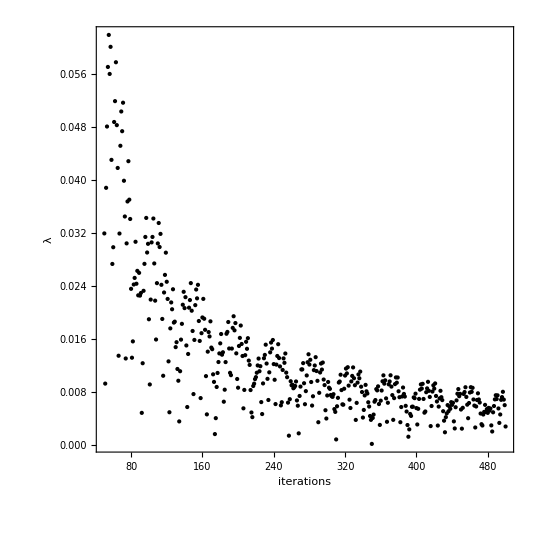

```mathematica
lyapunov[1, 1.5, 0, 2.57, .1,500]
```

```mathematica
lyapunovList
```

{{1,1.58739},{2,1.4744},{3,1.16491},{4,0.419075},{5,0.567877},{6,0.591792},{7,0.343645},{8,0.318028},{9,0.324721},{10,0.165713},{11,0.312651},{12,0.33638},{13,0.165616},{14,0.258487},{15,0.285932},{16,0.172396},{17,0.143497},{18,0.181102},{19,0.140134},{20,0.171767},{21,0.188934},{22,0.0978372},{23,0.170093},{24,0.1889},{25,0.107595},{26,0.156279},{27,0.173799},{28,0.118861},{29,0.0551742},{30,0.0760505},{31,0.0941953},{32,0.131158},{33,0.143576},{34,0.0844072},{35,0.129484},{36,0.143299},{37,0.09114},{38,0.114562},{39,0.129924},{40,0.0947723},{41,0.0825472},{42,0.0845702},{43,0.0669261},{44,0.102077},{45,0.113258},{46,0.0703019},{47,0.0974924},{48,0.109167},{49,0.0716917},{50,0.0873824},{51,0.0987061},{52,0.0751194},{53,0.0700249},{54,0.0748499},{55,0.0535138},{56,0.0836971},{57,0.0924028},{58,0.0587091},{59,0.0830119},{60,0.0921796},{61,0.0629475},{62,0.0712575},{63,0.0821946},{64,0.0646607},{65,0.0702756},{66,0.0757446},{67,0.0477632},{68,0.0732573},{69,0.0814062},{70,0.0544415},{71,0.0687181},{72,0.0772706},{73,0.0543552},{74,0.0561453},{75,0.0652259},{76,0.053416},{77,0.0598364},{78,0.0655485},{79,0.0414177},{80,0.062597},{81,0.0694065},{82,0.0463589},{83,0.061099},{84,0.0680295},{85,0.0489867},{86,0.0464142},{87,0.055978},{88,0.0476321},{89,0.0567176},{90,0.0616055},{91,0.0404288},{92,0.0571614},{93,0.0634966},{94,0.0438919},{95,0.0534148},{96,0.0601546},{97,0.0441874},{98,0.0365621},{99,0.0453321},{100,0.0407392}}